```mathematica
$PrePrint=Which[MatrixQ@#,Grid[#,Frame->All],VectorQ@#,Grid[{#},Frame->All],True,#]&;
```

## Задание 1. Полиномы.

```mathematica
ClearAll[L];
L[t_,0]=1;
L[t_,1]:=t;
L[t_,n_]/;n>1:=((2 n-1)/n t L[t,n-1]-(n-1)/n L[t,n-2])//Expand
```

```mathematica
L[t,5]
```

(15 t)/8-(35 t^3)/4+(63 t^5)/8

```mathematica
ClearAll[T];
T[t_,n_]:=Cos[n ArcCos[t]]//TrigExpand
```

```mathematica
t^#&/@Range[0,5]
L[t,#]&/@Range[0,5]
T[t,#]&/@Range[0,5]
```

1 | t | t^2 | t^3 | t^4 | t^5

1 | t | -1/2+(3 t^2)/2 | -(3 t)/2+(5 t^3)/2 | 3/8-(15 t^2)/4+(35 t^4)/8 | (15 t)/8-(35 t^3)/4+(63 t^5)/8

1 | t | -1+2 t^2 | -3 t+4 t^3 | 1-8 t^2+8 t^4 | 5 t-20 t^3+16 t^5

```mathematica
$PrePrint=.
```

```mathematica
RGBColor[#]&/@{{1,0.47,0.5},{0.51,0.84,0.5},{0.5,0.5,0.94},{0.5,0.84,0.95},{0.96,0.58,0.24},{0.79,0.85,0.35}}
```

{RGBColor[{1, 0.47, 0.5}],RGBColor[{0.51, 0.84, 0.5}],RGBColor[{0.5, 0.5, 0.94}],RGBColor[{0.5, 0.84, 0.95}],RGBColor[{0.96, 0.58, 0.24}],RGBColor[{0.79, 0.85, 0.35}]}

```mathematica
Subscript[ℒ, #][t]&/@Range[0,5]
```

{ℒ_0[t],ℒ_1[t],ℒ_2[t],ℒ_3[t],ℒ_4[t],ℒ_5[t]}

```mathematica
Subscript[𝒯, #][t]&/@Range[0,5]
```

{𝒯_0[t],𝒯_1[t],𝒯_2[t],𝒯_3[t],𝒯_4[t],𝒯_5[t]}

```mathematica
Manipulate[Plot[Полиномы,{t,-1,1},PlotLabel->Last@Most@Полиномы,PlotStyle->{RGBColor[{1, 0.47, 0.5}],RGBColor[{0.51, 0.84, 0.5}],RGBColor[{0.5, 0.5, 0.94}],RGBColor[{0.5, 0.84, 0.95}],RGBColor[{0.96, 0.58, 0.24}],RGBColor[{0.79, 0.85, 0.35}]},PlotLegends->Last@Полиномы,ImageSize->400],{Полиномы,{{1,t,t^2,t^3,t^4,t^5,"Степенные функции",{"1","t","t^2","t^3","t^4","t^5"}}->"Степенные функции",{1,t,-1/2+(3 t^2)/2,-(3 t)/2+(5 t^3)/2,3/8-(15 t^2)/4+(35 t^4)/8,(15 t)/8-(35 t^3)/4+(63 t^5)/8,"Полиномы Лежандра",{Subscript[ℒ, 0][t],Subscript[ℒ, 1][t],Subscript[ℒ, 2][t],Subscript[ℒ, 3][t],Subscript[ℒ, 4][t],Subscript[ℒ, 5][t]}}->"Лежандра",{1,t,-1+2 t^2,-3 t+4 t^3,1-8 t^2+8 t^4,5 t-20 t^3+16 t^5,"Полиномы Чебышева",{Subscript[𝒯, 0][t],Subscript[𝒯, 1][t],Subscript[𝒯, 2][t],Subscript[𝒯, 3][t],Subscript[𝒯, 4][t],Subscript[𝒯, 5][t]}}->"Чебышева"}}]
```

```mathematica
$PrePrint=Which[MatrixQ@#,Grid[#,Frame->All],VectorQ@#,Grid[{#},Frame->All],True,#]&;
```

```mathematica
ClearAll[kmPower,kmLegendre,kmChebyshev];
kmPower[t_]:=t^#&/@Range[0,5];
kmLegendre[t_]:=L[t,#]&/@Range[0,5];kmChebyshev[t_]:=T[t,#]&/@Range[0,5];
```

```mathematica
kmPower[t]
kmLegendre[t]
kmChebyshev[t]
```

1 | t | t^2 | t^3 | t^4 | t^5

1 | t | -1/2+(3 t^2)/2 | -(3 t)/2+(5 t^3)/2 | 3/8-(15 t^2)/4+(35 t^4)/8 | (15 t)/8-(35 t^3)/4+(63 t^5)/8

1 | t | -1+2 t^2 | -3 t+4 t^3 | 1-8 t^2+8 t^4 | 5 t-20 t^3+16 t^5

## Задание 2. Базисы векторного пространства полиномов.

```mathematica
Array[Subscript[x,#]&,6,0]
kmLegendre[t].%
Collect[%,t]
CoefficientList[%,t]
Thread[%==0]
Solve[%,%%%%%]
```

x_0 | x_1 | x_2 | x_3 | x_4 | x_5

x_0+t x_1+(-1/2+(3 t^2)/2) x_2+(-(3 t)/2+(5 t^3)/2) x_3+(3/8-(15 t^2)/4+(35 t^4)/8) x_4+((15 t)/8-(35 t^3)/4+(63 t^5)/8) x_5

x_0-x_2/2+t^2 ((3 x_2)/2-(15 x_4)/4)+(3 x_4)/8+(35 t^4 x_4)/8+t^3 ((5 x_3)/2-(35 x_5)/4)+(63 t^5 x_5)/8+t (x_1-(3 x_3)/2+(15 x_5)/8)

x_0-x_2/2+(3 x_4)/8 | x_1-(3 x_3)/2+(15 x_5)/8 | (3 x_2)/2-(15 x_4)/4 | (5 x_3)/2-(35 x_5)/4 | (35 x_4)/8 | (63 x_5)/8

x_0-x_2/2+(3 x_4)/8==0 | x_1-(3 x_3)/2+(15 x_5)/8==0 | (3 x_2)/2-(15 x_4)/4==0 | (5 x_3)/2-(35 x_5)/4==0 | (35 x_4)/8==0 | (63 x_5)/8==0

x_0→0 | x_1→0 | x_2→0 | x_3→0 | x_4→0 | x_5→0

```mathematica
Array[Subscript[x,#]&,6,0]
kmChebyshev[t].%
Collect[%,t]
CoefficientList[%,t]
Thread[%==0]
Solve[%,%%%%%]
```

x_0 | x_1 | x_2 | x_3 | x_4 | x_5

x_0+t x_1+(-1+2 t^2) x_2+(-3 t+4 t^3) x_3+(1-8 t^2+8 t^4) x_4+(5 t-20 t^3+16 t^5) x_5

x_0-x_2+t^2 (2 x_2-8 x_4)+x_4+8 t^4 x_4+t^3 (4 x_3-20 x_5)+16 t^5 x_5+t (x_1-3 x_3+5 x_5)

x_0-x_2+x_4 | x_1-3 x_3+5 x_5 | 2 x_2-8 x_4 | 4 x_3-20 x_5 | 8 x_4 | 16 x_5

x_0-x_2+x_4==0 | x_1-3 x_3+5 x_5==0 | 2 x_2-8 x_4==0 | 4 x_3-20 x_5==0 | 8 x_4==0 | 16 x_5==0

x_0→0 | x_1→0 | x_2→0 | x_3→0 | x_4→0 | x_5→0

```mathematica
Array[Subscript[x,#]&,6,0]
kmPower[t].%
Collect[%,t]
CoefficientList[%,t]
Thread[%==0]
Solve[%,%%%%%]
```

x_0 | x_1 | x_2 | x_3 | x_4 | x_5

x_0+t x_1+t^2 x_2+t^3 x_3+t^4 x_4+t^5 x_5

x_0+t x_1+t^2 x_2+t^3 x_3+t^4 x_4+t^5 x_5

x_0 | x_1 | x_2 | x_3 | x_4 | x_5

x_0==0 | x_1==0 | x_2==0 | x_3==0 | x_4==0 | x_5==0

x_0→0 | x_1→0 | x_2→0 | x_3→0 | x_4→0 | x_5→0

```mathematica
RandomReal[{-1,1},6]
```

-0.617881 | -0.946274 | -0.250341 | 0.667267 | 0.678264 | 0.310795

```mathematica
coord={0.729934, 0.296269,-0.352563,-0.242914,-0.228383,-0.167264}
```

0.729934 | 0.296269 | -0.352563 | -0.242914 | -0.228383 | -0.167264

```mathematica
pow=coord.kmPower[t]
leg=coord.kmLegendre[t]
cheb=coord.kmChebyshev[t]
```

0.729934+0.296269 t-0.352563 t^2-0.242914 t^3-0.228383 t^4-0.167264 t^5

0.729934+0.296269 t-0.352563 (-1/2+(3 t^2)/2)-0.242914 (-(3 t)/2+(5 t^3)/2)-0.228383 (3/8-(15 t^2)/4+(35 t^4)/8)-0.167264 ((15 t)/8-(35 t^3)/4+(63 t^5)/8)

0.729934+0.296269 t-0.352563 (-1+2 t^2)-0.242914 (-3 t+4 t^3)-0.228383 (1-8 t^2+8 t^4)-0.167264 (5 t-20 t^3+16 t^5)

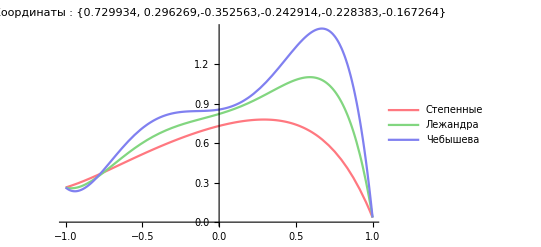

```mathematica
Plot[{pow,leg,cheb},{t,-1,1},PlotLabel->"Координаты :
 {0.729934, 0.296269,-0.352563,-0.242914,-0.228383,-0.167264} ",PlotLegends->MapThread[Style,{{"Степенные", "Лежандра", "Чебышева"},{RGBColor[{1, 0.47, 0.5}],RGBColor[{0.51, 0.84, 0.5}],RGBColor[{0.5, 0.5, 0.94}]}}],PlotStyle->{RGBColor[{1, 0.47, 0.5}],RGBColor[{0.51, 0.84, 0.5}],RGBColor[{0.5, 0.5, 0.94}]}]
```

```mathematica
MapThread[Style,{{"Степенные", "Лежандра", "Чебышева"},{RGBColor[{1, 0.47, 0.5}],RGBColor[{0.51, 0.84, 0.5}],RGBColor[{0.5, 0.5, 0.94}]}}]
```

Степенные | Лежандра | Чебышева

## Задание 3. Переход к другому базису.

```mathematica
kmPower[t]
kmLegendre[t]
kmChebyshev[t]
```

1 | t | t^2 | t^3 | t^4 | t^5

1 | t | -1/2+(3 t^2)/2 | -(3 t)/2+(5 t^3)/2 | 3/8-(15 t^2)/4+(35 t^4)/8 | (15 t)/8-(35 t^3)/4+(63 t^5)/8

1 | t | -1+2 t^2 | -3 t+4 t^3 | 1-8 t^2+8 t^4 | 5 t-20 t^3+16 t^5

```mathematica
$PrePrint=Which[MatrixQ@#,Grid[#,Frame->All],VectorQ@#,Grid[{#},Frame->All],True,#]&;
```

```mathematica
Outer[Subscript[a,StringJoin[#1,#2]]&,ToString/@Range[0,5],ToString/@Range[0,5]]
kmPower[t].%
Collect[%-kmLegendre[t],t]
CoefficientList[%,t]
Solve[%==Table[Table[0,6],6],%%%%//Flatten]

%%%%%/.%
MatrixForm@@%
```

a_00 | a_01 | a_02 | a_03 | a_04 | a_05
a_10 | a_11 | a_12 | a_13 | a_14 | a_15
a_20 | a_21 | a_22 | a_23 | a_24 | a_25
a_30 | a_31 | a_32 | a_33 | a_34 | a_35
a_40 | a_41 | a_42 | a_43 | a_44 | a_45
a_50 | a_51 | a_52 | a_53 | a_54 | a_55

a_00+t a_10+t^2 a_20+t^3 a_30+t^4 a_40+t^5 a_50 | a_01+t a_11+t^2 a_21+t^3 a_31+t^4 a_41+t^5 a_51 | a_02+t a_12+t^2 a_22+t^3 a_32+t^4 a_42+t^5 a_52 | a_03+t a_13+t^2 a_23+t^3 a_33+t^4 a_43+t^5 a_53 | a_04+t a_14+t^2 a_24+t^3 a_34+t^4 a_44+t^5 a_54 | a_05+t a_15+t^2 a_25+t^3 a_35+t^4 a_45+t^5 a_55

-1+a_00+t a_10+t^2 a_20+t^3 a_30+t^4 a_40+t^5 a_50 | a_01+t (-1+a_11)+t^2 a_21+t^3 a_31+t^4 a_41+t^5 a_51 | 1/2+a_02+t a_12+t^2 (-3/2+a_22)+t^3 a_32+t^4 a_42+t^5 a_52 | a_03+t (3/2+a_13)+t^2 a_23+t^3 (-5/2+a_33)+t^4 a_43+t^5 a_53 | -3/8+a_04+t a_14+t^2 (15/4+a_24)+t^3 a_34+t^4 (-35/8+a_44)+t^5 a_54 | a_05+t (-15/8+a_15)+t^2 a_25+t^3 (35/4+a_35)+t^4 a_45+t^5 (-63/8+a_55)

-1+a_00 | a_10 | a_20 | a_30 | a_40 | a_50
a_01 | -1+a_11 | a_21 | a_31 | a_41 | a_51
1/2+a_02 | a_12 | -3/2+a_22 | a_32 | a_42 | a_52
a_03 | 3/2+a_13 | a_23 | -5/2+a_33 | a_43 | a_53
-3/8+a_04 | a_14 | 15/4+a_24 | a_34 | -35/8+a_44 | a_54
a_05 | -15/8+a_15 | a_25 | 35/4+a_35 | a_45 | -63/8+a_55

a_00→1 | a_01→0 | a_02→-1/2 | a_03→0 | a_04→3/8 | a_05→0 | a_10→0 | a_11→1 | a_12→0 | a_13→-3/2 | a_14→0 | a_15→15/8 | a_20→0 | a_21→0 | a_22→3/2 | a_23→0 | a_24→-15/4 | a_25→0 | a_30→0 | a_31→0 | a_32→0 | a_33→5/2 | a_34→0 | a_35→-35/4 | a_40→0 | a_41→0 | a_42→0 | a_43→0 | a_44→35/8 | a_45→0 | a_50→0 | a_51→0 | a_52→0 | a_53→0 | a_54→0 | a_55→63/8

{{{1,0,-1/2,0,3/8,0},{0,1,0,-3/2,0,15/8},{0,0,3/2,0,-15/4,0},{0,0,0,5/2,0,-35/4},{0,0,0,0,35/8,0},{0,0,0,0,0,63/8}}}

(1 | 0 | -1/2 | 0 | 3/8 | 0
0 | 1 | 0 | -3/2 | 0 | 15/8
0 | 0 | 3/2 | 0 | -15/4 | 0
0 | 0 | 0 | 5/2 | 0 | -35/4
0 | 0 | 0 | 0 | 35/8 | 0
0 | 0 | 0 | 0 | 0 | 63/8)

```mathematica
PL=%
```

1 | 0 | -1/2 | 0 | 3/8 | 0
0 | 1 | 0 | -3/2 | 0 | 15/8
0 | 0 | 3/2 | 0 | -15/4 | 0
0 | 0 | 0 | 5/2 | 0 | -35/4
0 | 0 | 0 | 0 | 35/8 | 0
0 | 0 | 0 | 0 | 0 | 63/8

```mathematica
Outer[Subscript[a,StringJoin[#1,#2]]&,ToString/@Range[0,5],ToString/@Range[0,5]]
kmPower[t].%
Collect[%-kmChebyshev[t],t]
CoefficientList[%,t]
Solve[%==Table[Table[0,6],6],%%%%//Flatten]

%%%%%/.%
MatrixForm@@%
```

a_00 | a_01 | a_02 | a_03 | a_04 | a_05
a_10 | a_11 | a_12 | a_13 | a_14 | a_15
a_20 | a_21 | a_22 | a_23 | a_24 | a_25
a_30 | a_31 | a_32 | a_33 | a_34 | a_35
a_40 | a_41 | a_42 | a_43 | a_44 | a_45
a_50 | a_51 | a_52 | a_53 | a_54 | a_55

a_00+t a_10+t^2 a_20+t^3 a_30+t^4 a_40+t^5 a_50 | a_01+t a_11+t^2 a_21+t^3 a_31+t^4 a_41+t^5 a_51 | a_02+t a_12+t^2 a_22+t^3 a_32+t^4 a_42+t^5 a_52 | a_03+t a_13+t^2 a_23+t^3 a_33+t^4 a_43+t^5 a_53 | a_04+t a_14+t^2 a_24+t^3 a_34+t^4 a_44+t^5 a_54 | a_05+t a_15+t^2 a_25+t^3 a_35+t^4 a_45+t^5 a_55

-1+a_00+t a_10+t^2 a_20+t^3 a_30+t^4 a_40+t^5 a_50 | a_01+t (-1+a_11)+t^2 a_21+t^3 a_31+t^4 a_41+t^5 a_51 | 1+a_02+t a_12+t^2 (-2+a_22)+t^3 a_32+t^4 a_42+t^5 a_52 | a_03+t (3+a_13)+t^2 a_23+t^3 (-4+a_33)+t^4 a_43+t^5 a_53 | -1+a_04+t a_14+t^2 (8+a_24)+t^3 a_34+t^4 (-8+a_44)+t^5 a_54 | a_05+t (-5+a_15)+t^2 a_25+t^3 (20+a_35)+t^4 a_45+t^5 (-16+a_55)

-1+a_00 | a_10 | a_20 | a_30 | a_40 | a_50
a_01 | -1+a_11 | a_21 | a_31 | a_41 | a_51
1+a_02 | a_12 | -2+a_22 | a_32 | a_42 | a_52
a_03 | 3+a_13 | a_23 | -4+a_33 | a_43 | a_53
-1+a_04 | a_14 | 8+a_24 | a_34 | -8+a_44 | a_54
a_05 | -5+a_15 | a_25 | 20+a_35 | a_45 | -16+a_55

a_00→1 | a_01→0 | a_02→-1 | a_03→0 | a_04→1 | a_05→0 | a_10→0 | a_11→1 | a_12→0 | a_13→-3 | a_14→0 | a_15→5 | a_20→0 | a_21→0 | a_22→2 | a_23→0 | a_24→-8 | a_25→0 | a_30→0 | a_31→0 | a_32→0 | a_33→4 | a_34→0 | a_35→-20 | a_40→0 | a_41→0 | a_42→0 | a_43→0 | a_44→8 | a_45→0 | a_50→0 | a_51→0 | a_52→0 | a_53→0 | a_54→0 | a_55→16

{{{1,0,-1,0,1,0},{0,1,0,-3,0,5},{0,0,2,0,-8,0},{0,0,0,4,0,-20},{0,0,0,0,8,0},{0,0,0,0,0,16}}}

(1 | 0 | -1 | 0 | 1 | 0
0 | 1 | 0 | -3 | 0 | 5
0 | 0 | 2 | 0 | -8 | 0
0 | 0 | 0 | 4 | 0 | -20
0 | 0 | 0 | 0 | 8 | 0
0 | 0 | 0 | 0 | 0 | 16)

```mathematica
PT=%
```

1 | 0 | -1 | 0 | 1 | 0
0 | 1 | 0 | -3 | 0 | 5
0 | 0 | 2 | 0 | -8 | 0
0 | 0 | 0 | 4 | 0 | -20
0 | 0 | 0 | 0 | 8 | 0
0 | 0 | 0 | 0 | 0 | 16

## Задание 4. Матрица линейного отображения.

### a_0

```mathematica
Outer[Subscript[a,StringJoin[#1,#2]]&,ToString/@Range[0,5],ToString/@Range[0,5]];
kmPower[t].%;
Collect[%-kmPower[3t-2],t];
CoefficientList[%,t];
Solve[%==Table[Table[0,6],6],%%%%//Flatten];

%%%%%/.%;
MatrixForm@@%
```

(1 | -2 | 4 | -8 | 16 | -32
0 | 3 | -12 | 36 | -96 | 240
0 | 0 | 9 | -54 | 216 | -720
0 | 0 | 0 | 27 | -216 | 1080
0 | 0 | 0 | 0 | 81 | -810
0 | 0 | 0 | 0 | 0 | 243)

```mathematica
Subscript[Pa, 0]=%
```

1 | -2 | 4 | -8 | 16 | -32
0 | 3 | -12 | 36 | -96 | 240
0 | 0 | 9 | -54 | 216 | -720
0 | 0 | 0 | 27 | -216 | 1080
0 | 0 | 0 | 0 | 81 | -810
0 | 0 | 0 | 0 | 0 | 243

```mathematica
Outer[Subscript[a,StringJoin[#1,#2]]&,ToString/@Range[0,5],ToString/@Range[0,5]];
kmLegendre[t].%;
Collect[%-kmLegendre[3t-2],t];
CoefficientList[%,t];
Solve[%==Table[Table[0,6],6],%%%%//Flatten];

%%%%%/.%;
MatrixForm@@%
```

(1 | -2 | 10 | -62 | 430 | -3194
0 | 3 | -18 | 126 | -942 | 7362
0 | 0 | 9 | -90 | 810 | -7110
0 | 0 | 0 | 27 | -378 | 4158
0 | 0 | 0 | 0 | 81 | -1458
0 | 0 | 0 | 0 | 0 | 243)

```mathematica
Subscript[La, 0]=%
```

1 | -2 | 10 | -62 | 430 | -3194
0 | 3 | -18 | 126 | -942 | 7362
0 | 0 | 9 | -90 | 810 | -7110
0 | 0 | 0 | 27 | -378 | 4158
0 | 0 | 0 | 0 | 81 | -1458
0 | 0 | 0 | 0 | 0 | 243

```mathematica
Outer[Subscript[a,StringJoin[#1,#2]]&,ToString/@Range[0,5],ToString/@Range[0,5]];
kmChebyshev[t].%;
Collect[%-kmChebyshev[3t-2],t];
CoefficientList[%,t];
Solve[%==Table[Table[0,6],6],%%%%//Flatten];

%%%%%/.%;
MatrixForm@@%
```

(1 | -2 | 16 | -134 | 1168 | -10442
0 | 3 | -24 | 216 | -1968 | 18120
0 | 0 | 9 | -108 | 1152 | -11700
0 | 0 | 0 | 27 | -432 | 5400
0 | 0 | 0 | 0 | 81 | -1620
0 | 0 | 0 | 0 | 0 | 243)

```mathematica
Subscript[Ta, 0]=%
```

1 | -2 | 16 | -134 | 1168 | -10442
0 | 3 | -24 | 216 | -1968 | 18120
0 | 0 | 9 | -108 | 1152 | -11700
0 | 0 | 0 | 27 | -432 | 5400
0 | 0 | 0 | 0 | 81 | -1620
0 | 0 | 0 | 0 | 0 | 243

### a_1

```mathematica
Outer[Subscript[a,StringJoin[#1,#2]]&,ToString/@Range[0,5],ToString/@Range[0,5]];
kmChebyshev[t].%;
Collect[%-D[kmChebyshev[t],t],t];
CoefficientList[%,t];
Solve[%==Table[Table[0,6],6],%%%%//Flatten];

%%%%%/.%;
MatrixForm@@%
```

(0 | 1 | 0 | 3 | 0 | 5
0 | 0 | 4 | 0 | 8 | 0
0 | 0 | 0 | 6 | 0 | 10
0 | 0 | 0 | 0 | 8 | 0
0 | 0 | 0 | 0 | 0 | 10
0 | 0 | 0 | 0 | 0 | 0)

```mathematica
Subscript[Ta, 1]=%
```

0 | 1 | 0 | 3 | 0 | 5
0 | 0 | 4 | 0 | 8 | 0
0 | 0 | 0 | 6 | 0 | 10
0 | 0 | 0 | 0 | 8 | 0
0 | 0 | 0 | 0 | 0 | 10
0 | 0 | 0 | 0 | 0 | 0

```mathematica
Outer[Subscript[a,StringJoin[#1,#2]]&,ToString/@Range[0,5],ToString/@Range[0,5]];
kmLegendre[t].%;
Collect[%-D[kmLegendre[t],t],t];
CoefficientList[%,t];
Solve[%==Table[Table[0,6],6],%%%%//Flatten];

%%%%%/.%;
MatrixForm@@%
```

(0 | 1 | 0 | 1 | 0 | 1
0 | 0 | 3 | 0 | 3 | 0
0 | 0 | 0 | 5 | 0 | 5
0 | 0 | 0 | 0 | 7 | 0
0 | 0 | 0 | 0 | 0 | 9
0 | 0 | 0 | 0 | 0 | 0)

```mathematica
Subscript[La, 1]=%
```

0 | 1 | 0 | 1 | 0 | 1
0 | 0 | 3 | 0 | 3 | 0
0 | 0 | 0 | 5 | 0 | 5
0 | 0 | 0 | 0 | 7 | 0
0 | 0 | 0 | 0 | 0 | 9
0 | 0 | 0 | 0 | 0 | 0

```mathematica
Outer[Subscript[a,StringJoin[#1,#2]]&,ToString/@Range[0,5],ToString/@Range[0,5]];
kmPower[t].%;
Collect[%-D[kmPower[t],t],t];
CoefficientList[%,t];
Solve[%==Table[Table[0,6],6],%%%%//Flatten];

%%%%%/.%;
MatrixForm@@%
```

(0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 2 | 0 | 0 | 0
0 | 0 | 0 | 3 | 0 | 0
0 | 0 | 0 | 0 | 4 | 0
0 | 0 | 0 | 0 | 0 | 5
0 | 0 | 0 | 0 | 0 | 0)

```mathematica
Subscript[Pa, 1]=%
```

0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 2 | 0 | 0 | 0
0 | 0 | 0 | 3 | 0 | 0
0 | 0 | 0 | 0 | 4 | 0
0 | 0 | 0 | 0 | 0 | 5
0 | 0 | 0 | 0 | 0 | 0

### a_h

```mathematica
Outer[Subscript[a,StringJoin[#1,#2]]&,ToString/@Range[0,5],ToString/@Range[0,5]];
kmPower[t].%;
Collect[%-((kmPower[t+h]-kmPower[t])/h),t];
CoefficientList[%,t];
Solve[%==Table[Table[0,6],6],%%%%//Flatten];

%%%%%/.%;
MatrixForm@@%
```

(0 | 1 | h | h^2 | h^3 | h^4
0 | 0 | 2 | 3 h | 4 h^2 | 5 h^3
0 | 0 | 0 | 3 | 6 h | 10 h^2
0 | 0 | 0 | 0 | 4 | 10 h
0 | 0 | 0 | 0 | 0 | 5
0 | 0 | 0 | 0 | 0 | 0)

```mathematica
Subscript[Pa, h]=%
```

0 | 1 | h | h^2 | h^3 | h^4
0 | 0 | 2 | 3 h | 4 h^2 | 5 h^3
0 | 0 | 0 | 3 | 6 h | 10 h^2
0 | 0 | 0 | 0 | 4 | 10 h
0 | 0 | 0 | 0 | 0 | 5
0 | 0 | 0 | 0 | 0 | 0

```mathematica
Outer[Subscript[a,StringJoin[#1,#2]]&,ToString/@Range[0,5],ToString/@Range[0,5]];
kmChebyshev[t].%;
Collect[%-((kmChebyshev[t+h]-kmChebyshev[t])/h),t];
CoefficientList[%,t];
Solve[%==Table[Table[0,6],6],%%%%//Flatten];

%%%%%/.%;
MatrixForm@@%
```

(0 | 1 | 2 h | 3+4 h^2 | 8 (2 h+h^3) | 5+60 h^2+16 h^4
0 | 0 | 4 | 12 h | 8 (1+4 h^2) | 20 (3 h+4 h^3)
0 | 0 | 0 | 6 | 24 h | 10 (1+8 h^2)
0 | 0 | 0 | 0 | 8 | 40 h
0 | 0 | 0 | 0 | 0 | 10
0 | 0 | 0 | 0 | 0 | 0)

```mathematica
Subscript[Ta, h]=%
```

0 | 1 | 2 h | 3+4 h^2 | 8 (2 h+h^3) | 5+60 h^2+16 h^4
0 | 0 | 4 | 12 h | 8 (1+4 h^2) | 20 (3 h+4 h^3)
0 | 0 | 0 | 6 | 24 h | 10 (1+8 h^2)
0 | 0 | 0 | 0 | 8 | 40 h
0 | 0 | 0 | 0 | 0 | 10
0 | 0 | 0 | 0 | 0 | 0

```mathematica
Outer[Subscript[a,StringJoin[#1,#2]]&,ToString/@Range[0,5],ToString/@Range[0,5]];
kmLegendre[t].%;
Collect[%-((kmLegendre[t+h]-kmLegendre[t])/h),t];
CoefficientList[%,t];
Solve[%==Table[Table[0,6],6],%%%%//Flatten];

%%%%%/.%;
MatrixForm@@%
```

(0 | 1 | (3 h)/2 | 1/2 (2+5 h^2) | 5/8 (8 h+7 h^3) | 1/8 (8+140 h^2+63 h^4)
0 | 0 | 3 | (15 h)/2 | 1/2 (6+35 h^2) | 21/8 (8 h+15 h^3)
0 | 0 | 0 | 5 | (35 h)/2 | 5/2 (2+21 h^2)
0 | 0 | 0 | 0 | 7 | (63 h)/2
0 | 0 | 0 | 0 | 0 | 9
0 | 0 | 0 | 0 | 0 | 0)

```mathematica
Subscript[La, h]=%
```

0 | 1 | (3 h)/2 | 1/2 (2+5 h^2) | 5/8 (8 h+7 h^3) | 1/8 (8+140 h^2+63 h^4)
0 | 0 | 3 | (15 h)/2 | 1/2 (6+35 h^2) | 21/8 (8 h+15 h^3)
0 | 0 | 0 | 5 | (35 h)/2 | 5/2 (2+21 h^2)
0 | 0 | 0 | 0 | 7 | (63 h)/2
0 | 0 | 0 | 0 | 0 | 9
0 | 0 | 0 | 0 | 0 | 0

### a_2

```mathematica
Outer[Subscript[a,StringJoin[#1,#2]]&,ToString/@Range[0,5],ToString/@Range[0,5]];
kmLegendre[t].%;
Collect[%-(kmLegendre[2 t+1]-2 D[kmLegendre[t],t]),t];
CoefficientList[%,t];
Solve[%==Table[Table[0,6],6],%%%%//Flatten];

%%%%%/.%;
MatrixForm@@%
```

(1 | -1 | 3 | 9 | 45 | 195
0 | 2 | 0 | 24 | 98 | 474
0 | 0 | 4 | 10 | 100 | 490
0 | 0 | 0 | 8 | 42 | 336
0 | 0 | 0 | 0 | 16 | 126
0 | 0 | 0 | 0 | 0 | 32)

```mathematica
Subscript[La, 2]=%
```

1 | -1 | 3 | 9 | 45 | 195
0 | 2 | 0 | 24 | 98 | 474
0 | 0 | 4 | 10 | 100 | 490
0 | 0 | 0 | 8 | 42 | 336
0 | 0 | 0 | 0 | 16 | 126
0 | 0 | 0 | 0 | 0 | 32

```mathematica
Outer[Subscript[a,StringJoin[#1,#2]]&,ToString/@Range[0,5],ToString/@Range[0,5]];
kmPower[t].%;
Collect[%-(kmPower[2 t+1]-2 D[kmPower[t],t]),t];
CoefficientList[%,t];
Solve[%==Table[Table[0,6],6],%%%%//Flatten];

%%%%%/.%;
MatrixForm@@%
```

(1 | -1 | 1 | 1 | 1 | 1
0 | 2 | 0 | 6 | 8 | 10
0 | 0 | 4 | 6 | 24 | 40
0 | 0 | 0 | 8 | 24 | 80
0 | 0 | 0 | 0 | 16 | 70
0 | 0 | 0 | 0 | 0 | 32)

```mathematica
Subscript[Pa, 2]=%
```

1 | -1 | 1 | 1 | 1 | 1
0 | 2 | 0 | 6 | 8 | 10
0 | 0 | 4 | 6 | 24 | 40
0 | 0 | 0 | 8 | 24 | 80
0 | 0 | 0 | 0 | 16 | 70
0 | 0 | 0 | 0 | 0 | 32

```mathematica
Outer[Subscript[a,StringJoin[#1,#2]]&,ToString/@Range[0,5],ToString/@Range[0,5]];
kmChebyshev[t].%;
Collect[%-(kmChebyshev[2 t+1]-2 D[kmChebyshev[t],t]),t];
CoefficientList[%,t];
Solve[%==Table[Table[0,6],6],%%%%//Flatten];

%%%%%/.%;
MatrixForm@@%
```

(1 | -1 | 5 | 19 | 129 | 671
0 | 2 | 0 | 42 | 208 | 1210
0 | 0 | 4 | 12 | 144 | 820
0 | 0 | 0 | 8 | 48 | 440
0 | 0 | 0 | 0 | 16 | 140
0 | 0 | 0 | 0 | 0 | 32)

```mathematica
Subscript[Ta, 2]=%
```

1 | -1 | 5 | 19 | 129 | 671
0 | 2 | 0 | 42 | 208 | 1210
0 | 0 | 4 | 12 | 144 | 820
0 | 0 | 0 | 8 | 48 | 440
0 | 0 | 0 | 0 | 16 | 140
0 | 0 | 0 | 0 | 0 | 32

```mathematica
Subscript[Pa, 0]
Subscript[Ta, 0]
Subscript[La, 0]
```

1 | -2 | 4 | -8 | 16 | -32
0 | 3 | -12 | 36 | -96 | 240
0 | 0 | 9 | -54 | 216 | -720
0 | 0 | 0 | 27 | -216 | 1080
0 | 0 | 0 | 0 | 81 | -810
0 | 0 | 0 | 0 | 0 | 243

1 | -2 | 16 | -134 | 1168 | -10442
0 | 3 | -24 | 216 | -1968 | 18120
0 | 0 | 9 | -108 | 1152 | -11700
0 | 0 | 0 | 27 | -432 | 5400
0 | 0 | 0 | 0 | 81 | -1620
0 | 0 | 0 | 0 | 0 | 243

1 | -2 | 10 | -62 | 430 | -3194
0 | 3 | -18 | 126 | -942 | 7362
0 | 0 | 9 | -90 | 810 | -7110
0 | 0 | 0 | 27 | -378 | 4158
0 | 0 | 0 | 0 | 81 | -1458
0 | 0 | 0 | 0 | 0 | 243

```mathematica
Subscript[Pa, 1]
Subscript[Ta, 1]
Subscript[La, 1]
```

0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 2 | 0 | 0 | 0
0 | 0 | 0 | 3 | 0 | 0
0 | 0 | 0 | 0 | 4 | 0
0 | 0 | 0 | 0 | 0 | 5
0 | 0 | 0 | 0 | 0 | 0

0 | 1 | 0 | 3 | 0 | 5
0 | 0 | 4 | 0 | 8 | 0
0 | 0 | 0 | 6 | 0 | 10
0 | 0 | 0 | 0 | 8 | 0
0 | 0 | 0 | 0 | 0 | 10
0 | 0 | 0 | 0 | 0 | 0

0 | 1 | 0 | 1 | 0 | 1
0 | 0 | 3 | 0 | 3 | 0
0 | 0 | 0 | 5 | 0 | 5
0 | 0 | 0 | 0 | 7 | 0
0 | 0 | 0 | 0 | 0 | 9
0 | 0 | 0 | 0 | 0 | 0

```mathematica
Subscript[Pa, h]
Subscript[Ta, h]
Subscript[La, h]
```

0 | 1 | h | h^2 | h^3 | h^4
0 | 0 | 2 | 3 h | 4 h^2 | 5 h^3
0 | 0 | 0 | 3 | 6 h | 10 h^2
0 | 0 | 0 | 0 | 4 | 10 h
0 | 0 | 0 | 0 | 0 | 5
0 | 0 | 0 | 0 | 0 | 0

0 | 1 | 2 h | 3+4 h^2 | 8 (2 h+h^3) | 5+60 h^2+16 h^4
0 | 0 | 4 | 12 h | 8 (1+4 h^2) | 20 (3 h+4 h^3)
0 | 0 | 0 | 6 | 24 h | 10 (1+8 h^2)
0 | 0 | 0 | 0 | 8 | 40 h
0 | 0 | 0 | 0 | 0 | 10
0 | 0 | 0 | 0 | 0 | 0

0 | 1 | (3 h)/2 | 1/2 (2+5 h^2) | 5/8 (8 h+7 h^3) | 1/8 (8+140 h^2+63 h^4)
0 | 0 | 3 | (15 h)/2 | 1/2 (6+35 h^2) | 21/8 (8 h+15 h^3)
0 | 0 | 0 | 5 | (35 h)/2 | 5/2 (2+21 h^2)
0 | 0 | 0 | 0 | 7 | (63 h)/2
0 | 0 | 0 | 0 | 0 | 9
0 | 0 | 0 | 0 | 0 | 0

```mathematica
Subscript[Pa, 2]
Subscript[Ta, 2]
Subscript[La, 2]
```

1 | -1 | 1 | 1 | 1 | 1
0 | 2 | 0 | 6 | 8 | 10
0 | 0 | 4 | 6 | 24 | 40
0 | 0 | 0 | 8 | 24 | 80
0 | 0 | 0 | 0 | 16 | 70
0 | 0 | 0 | 0 | 0 | 32

1 | -1 | 5 | 19 | 129 | 671
0 | 2 | 0 | 42 | 208 | 1210
0 | 0 | 4 | 12 | 144 | 820
0 | 0 | 0 | 8 | 48 | 440
0 | 0 | 0 | 0 | 16 | 140
0 | 0 | 0 | 0 | 0 | 32

1 | -1 | 3 | 9 | 45 | 195
0 | 2 | 0 | 24 | 98 | 474
0 | 0 | 4 | 10 | 100 | 490
0 | 0 | 0 | 8 | 42 | 336
0 | 0 | 0 | 0 | 16 | 126
0 | 0 | 0 | 0 | 0 | 32

```mathematica
({{0, 1, 0, 0, 0, 0}, {0, 0, 2, 0, 0, 0}, {0, 0, 0, 3, 0, 0}, {0, 0, 0, 0, 4, 0}, {0, 0, 0, 0, 0, 5}, {0, 0, 0, 0, 0, 0}}).({{1}, {-1}, {5}, {4}, {3}, {2}})
```

-1
10
12
12
10
0

2 x^5 + 3 x^4 + 4 x^3 + 5 x^2 - x + 1 ->(D)->0 x^5+10 x^4+12 x^3+12 x^2+10x-1

```mathematica
({{0, 1, 2h, 3+4 h^2, 8 (2 h+h^3), 5+60 h^2+16 h^4}, {0, 0, 4, 12 h, 8 (1+4 h^2), 20 (3 h+4 h^3)}, {0, 0, 0, 6, 24 h, 10 (1+8 h^2)}, {0, 0, 0, 0, 8, 40 h}, {0, 0, 0, 0, 0, 10}, {0, 0, 0, 0, 0, 0}}).({{1}, {-1}, {5}, {4}, {3}, {2}})
%/.h->0
```

-1+10 h+4 (3+4 h^2)+24 (2 h+h^3)+2 (5+60 h^2+16 h^4)
20+48 h+24 (1+4 h^2)+40 (3 h+4 h^3)
24+72 h+20 (1+8 h^2)
24+80 h
20
0

21
44
44
24
20
0

```mathematica
({{0, 1, 0, 3, 0, 5}, {0, 0, 4, 0, 8, 0}, {0, 0, 0, 6, 0, 10}, {0, 0, 0, 0, 8, 0}, {0, 0, 0, 0, 0, 10}, {0, 0, 0, 0, 0, 0}}).({{1}, {-1}, {5}, {4}, {3}, {2}})
```

21
44
44
24
20
0

A_h/. h→0 = A_1

## Задание 5. Векторное пространство линейных функционалов.

### a_0

```mathematica
kmPower[1/2]
kmLegendre[1/2]
kmChebyshev[1/2]
```

1 | 1/2 | 1/4 | 1/8 | 1/16 | 1/32

1 | 1/2 | -1/8 | -7/16 | -37/128 | 23/256

1 | 1/2 | -1/2 | -1 | -1/2 | 1/2

### a_1

```mathematica
ReplaceAll[D[#,t]&/@
{kmPower[t],
kmLegendre[t],
kmChebyshev[t]},t->1]
```

0 | 1 | 2 | 3 | 4 | 5
0 | 1 | 3 | 6 | 10 | 15
0 | 1 | 4 | 9 | 16 | 25

### a_2

```mathematica
(#[1]-#[-1])/2&/@{kmPower,
kmLegendre,
kmChebyshev}
```

0 | 1 | 0 | 1 | 0 | 1
0 | 1 | 0 | 1 | 0 | 1
0 | 1 | 0 | 1 | 0 | 1

Проверим правила преобразования координат линейного функционала.

```mathematica
{1,1/2,-1/8,-7/16,-37/128,23/256}=={1,1/2,1/4,1/8,1/16,1/32}.PL
```

True

```mathematica
{1,1/2,-1/2,-1,-1/2,1/2}=={1,1/2,1/4,1/8,1/16,1/32}.PT
```

True

```mathematica
{0,1,3,6,10,15}=={0,1,2,3,4,5}.PL
```

True

```mathematica
{0,1,4,9,16,25}=={0,1,2,3,4,5}.PT
```

True

```mathematica
{0,1,0,1,0,1}=={0,1,0,1,0,1}.PT
```

True

```mathematica
{0,1,0,1,0,1}=={0,1,0,1,0,1}.PL
```

True

## Задание 6. Ковариантные и контравариантные объекты.

Любой вектор, так же как и линейный функционал, задается набором координат. Координаты вектора принято записывать в столбец,  а координаты линейного функционала в строку. Отличие линейного функционала от  вектора также заключается в правиле преобразования координат :  при смене базиса координаты ковектора преобразуются как базис, в отличие от координат векторов, преобразующихся противоположно базису.